```mathematica
rgb=<<"~/Yandex.Disk/Documents/research/kiaa/stgbns/expgb.txt";
```

```mathematica
rgbss=Simplify[rgb/.{epp->0,Derivative[0,1][nuf][r,th]->0,Derivative[1,1][nuf][r,th]->0,Derivative[0,2][nuf][r,th]->0,Derivative[0,1][mu1f][r,th]->0,Derivative[1,1][mu1f][r,th]->0,Derivative[0,2][mu1f][r,th]->0,mu2f[r,th]->Log[r],Derivative[0,1][mu2f][r,th]->0,Derivative[1,1][mu2f][r,th]->0,Derivative[0,2][mu2f][r,th]->0,Derivative[1,0][mu2f][r,th]->D[Log[r],r],Derivative[2,0][mu2f][r,th]->D[Log[r],r,r],psf[r,th]->Log[r*Sin[th]],Derivative[0,1][psf][r,th]->D[Log[r*Sin[th]],th],Derivative[1,1][psf][r,th]->D[Log[r*Sin[th]],r,th],Derivative[0,2][psf][r,th]->D[Log[r*Sin[th]],th,th],Derivative[1,0][psf][r,th]->D[Log[r*Sin[th]],r],Derivative[2,0][psf][r,th]->D[Log[r*Sin[th]],r,r]}]
```

1/r^2 8 ⅇ^(-4 mu1f[r,th]) ((-3+ⅇ^(2 mu1f[r,th])) mu1f^(1,0)[r,th] nuf^(1,0)[r,th]-(-1+ⅇ^(2 mu1f[r,th])) ((nuf^(1,0)[r,th])^2+nuf^(2,0)[r,th]))

```mathematica
nur=4*Pi*r^2*p[r]/(r-2*m[r])+m[r]/(r*(r-2*m[r]));mr=4*Pi*r^2*ep[r];pr=-(ep[r]+p[r])*nur;
```

```mathematica
rgbss1=Simplify[rgbss/.{mu1f[r,th]->-1/2*Log[1-2*m[r]/r],Derivative[1,0][mu1f][r,th]->D[-1/2*Log[1-2*m[r]/r],r],Derivative[1,0][nuf][r,th]->nur,Derivative[2,0][nuf][r,th]->D[nur,r]}/.{m'[r]->mr,p'[r]->pr}]
```

-(16 (-3 m[r]^2+8 π r^3 ep[r] (m[r]+2 π r^3 p[r])))/r^6

```mathematica
(* expansion at the center *)
```

```mathematica
D[mr,r,r]/.{r->0}
```

8 π ep[0]

```mathematica
D[mr,r,r,r]/.{r->0}
```

24 π ep'[0]

```mathematica
D[mr,r,r,r,r]/.{r->0}
```

48 π ep''[0]

```mathematica
Simplify[pr/.{m[r]->4/3*Pi*ep[0]*r^3}]/.r->0
```

0

```mathematica
prr=Simplify[D[pr,r]/.{m'[r]->mr,p'[r]->pr}]
```

1/(r^2 (r-2 m[r])^2)(-4 π r^3 ep[r]^2 (r-m[r]+4 π r^3 p[r])+ep[r] (-m[r]^2+8 π r^4 p[r] (-1+2 π r^2 p[r])+2 m[r] (r+16 π r^3 p[r]))-m[r]^2 (p[r]-2 r ep'[r])+4 π r^4 p[r] (-p[r]+8 π r^2 p[r]^2-r ep'[r])+r m[r] (28 π r^2 p[r]^2-r ep'[r]+p[r] (2+8 π r^3 ep'[r])))

```mathematica
Simplify[Simplify[prr/.m[r]->4/3*Pi*ep[0]*r^3]/.{r->0}]
```

-4/3 π (ep[0]^2+4 ep[0] p[0]+3 p[0]^2)

```mathematica
afr=r-2*m[r];bfr=2*(1-m[r]/r)-4*Pi*r^2*(ep[r]-p[r]);cfr=r*(f2*rgbss1-u2);
```

```mathematica
(* a *)
```

```mathematica
Simplify[afr/.{m[r]->4/3*Pi*ep[0]*r^3+2/5*Pi*ep''[0]*r^5}]
```

r-8/3 π r^3 ep[0]-4/5 π r^5 ep''[0]

```mathematica
(* b *)
```

```mathematica
bfr2=Simplify[bfr/.{m[r]->4/3*Pi*ep[0]*r^3+2/5*Pi*ep''[0]*r^5,ep[r]->ep[0]+1/2*ep''[0]*r^2,p[r]->p[0]+1/2*p''[0]*r^2}]
```

2+π r^2 (-(20 ep[0])/3+4 p[0]+r^2 (-14/5 ep''[0]+2 p''[0]))

```mathematica
Coefficient[bfr2,r,4]
```

-14/5 π ep''[0]+2 π p''[0]

```mathematica
(* c *)
```

```mathematica
cfr2=Simplify[cfr/.{m[r]->4/3*Pi*ep[0]*r^3+2/5*Pi*ep''[0]*r^5,ep[r]->ep[0]+1/2*ep''[0]*r^2,p[r]->p[0]+1/2*p''[0]*r^2}]
```

-1/75 r (75 u2+64 f2 π^2 (100 ep[0]^2+50 ep[0] (6 p[0]+r^2 (2 ep''[0]+3 p''[0]))+3 r^2 ep''[0] (50 p[0]+r^2 (7 ep''[0]+25 p''[0]))))

```mathematica
Simplify[Coefficient[cfr2,r,3]]
```

-128/3 f2 π^2 (3 p[0] ep''[0]+ep[0] (2 ep''[0]+3 p''[0]))

```mathematica
rgbss1
```

-(16 (-3 m[r]^2+8 π r^3 ep[r] (m[r]+2 π r^3 p[r])))/r^6

```mathematica
(* numerical solution *)
```

```mathematica
rgbss2=(48*y^2)/x^6-(32*w*(y+1/2*v*x^3))/x^3;scalareq=(1-2*y/x)*bph''[x]+(1-(2*y)/x)*(2/(x-2y)*(1-y/x)-(x^2*(w-v))/(x-2y))*bph'[x]+(f2*rgbss2-u2)*bph[x];
```

```mathematica
(* exterior *)
```

```mathematica
scalareqex=Simplify[scalareq/.{w->0,v->0,y->ym}]
```

((-u2 x^6+48 f2 ym^2) bph[x]+x^4 (2 (x-ym) bph'[x]+x (x-2 ym) bph''[x]))/x^6

```mathematica
xf1=100;
```

```mathematica
ym1=ymset[[100]];f21=7;u21=3;scalareqex1=scalareqex/.{ym->ym1,f2->f21,u2->u21}
```

((83.6643-3 x^6) bph[x]+x^4 (2 (-0.499+x) bph'[x]+(-0.998+x) x bph''[x]))/x^6

```mathematica
solex=NDSolve[{scalareqex1==0,bph[1]==1,bph'[1]==650},bph,{x,1,xf1}]
```

{{bph→InterpolatingFunction[{{1., 100.}}, <>]}}

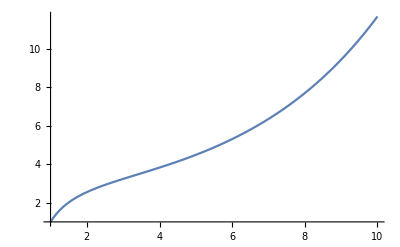

```mathematica
Plot[bph[x]/.solex,{x,1,10}]
```

```mathematica
xtail=100;tail=100;
bphpshoottest=1000;
While[bphpshoottest>-1000,
solex=NDSolve[{scalareqex1==0,bph[1]==1,bph'[1]==bphpshoottest},bph,{x,1,xtail}];tail=bph[x]/.solex[[1]]/.x->xtail;Print[tail,",",bphpshoottest];bphpshoottest=bphpshoottest-50];
```

-2.29963×10^73,1000

-2.26334×10^73,950

-2.22704×10^73,900

-2.19074×10^73,850

-2.15444×10^73,800

-2.11814×10^73,750

-2.08185×10^73,700

-2.04555×10^73,650

-2.00925×10^73,600

-1.97295×10^73,550

-1.93666×10^73,500

-1.90036×10^73,450

-1.86406×10^73,400

-1.82776×10^73,350

-1.79146×10^73,300

-1.75517×10^73,250

-1.71887×10^73,200

-1.68257×10^73,150

-1.64627×10^73,100

-1.60997×10^73,50

-1.57368×10^73,0

-1.53738×10^73,-50

-1.50108×10^73,-100

-1.46478×10^73,-150

-1.42848×10^73,-200

-1.39219×10^73,-250

-1.35589×10^73,-300

-1.31959×10^73,-350

-1.28329×10^73,-400

-1.24699×10^73,-450

-1.2107×10^73,-500

-1.1744×10^73,-550

-1.1381×10^73,-600

-1.1018×10^73,-650

-1.0655×10^73,-700

-1.02921×10^73,-750

-9.92912×10^72,-800

-9.5661×10^72,-850

-9.20312×10^72,-900

-8.84013×10^72,-950

```mathematica
xtail=100;tail=100;bphpshootl=50;bphpshooth=-50;
bphpshoottest=bphpshootl;j=0;
While[Abs[bphpshoottest-N[(bphpshootl+bphpshooth)/2]]>10^-6&&j<1000,bphpshoottest=N[(bphpshootl+bphpshooth)/2];scalareqex1=scalareqex/.{ym->ym1,f2->f21,u2->u21};
solex=NDSolve[{scalareqex1==0,bph[1]==1,bph'[1]==bphpshoottest},bph,{x,1,xtail}];tail=bph[x]/.solex[[1]]/.x->xtail;Print[tail,",",bphpshoottest];
If[tail>0,bphpshootl=bphpshoottest,bphpshooth=bphpshoottest];j++];
```

8.5956×10^11,0.

-1.46541×10^13,-25.

-6.89729×10^12,-12.5

-3.01887×10^12,-6.25

-1.07965×10^12,-3.125

-1.10048×10^11,-1.5625

3.74756×10^11,-0.78125

1.32354×10^11,-1.17188

1.11531×10^10,-1.36719

-4.94473×10^10,-1.46484

-1.91471×10^10,-1.41602

-3.99697×10^9,-1.3916

3.57809×10^9,-1.37939

-2.09441×10^8,-1.3855

1.68432×10^9,-1.38245

7.37443×10^8,-1.38397

2.64002×10^8,-1.38474

2.72808×10^7,-1.38512

-9.10806×10^7,-1.38531

-3.19001×10^7,-1.38521

-2.30984×10^6,-1.38516

1.24856×10^7,-1.38514

5.08788×10^6,-1.38515

1.38908×10^6,-1.38516

-460410.,-1.38516

464400.,-1.38516

```mathematica
ncpt=100;f2set={0.8};u2set={0.1};ymset=Table[ymmin+(ymmax-ymmin)/(ncpt-1)*(i-1),{i,1,ncpt}];bphpexset=Table[0,{i,1,ncpt},{jr,1,Length[f2set]},{kr,1,Length[u2set]}];
```

```mathematica
AbsoluteTiming[xtail=100;tail=100;Do[bphpshootl=50;bphpshooth=-50;bphpshoottest=bphpshootl;j=0;
While[Abs[bphpshoottest-N[(bphpshootl+bphpshooth)/2]]>10^-6&&j<1000,bphpshoottest=N[(bphpshootl+bphpshooth)/2];scalareqex1=scalareqex/.{ym->ymset[[i]],f2->f2set[[1]],u2->u2set[[1]]};
solex=NDSolve[{scalareqex1==0,bph[1]==1,bph'[1]==bphpshoottest},bph,{x,1,xtail}];tail=bph[x]/.solex[[1]]/.x->xtail;
If[tail>0,bphpshootl=bphpshoottest,bphpshooth=bphpshoottest];j++];bphpexset[[i,1,1]]=bphpshoottest,{i,1,ncpt}];]
```

{8.84128,Null}

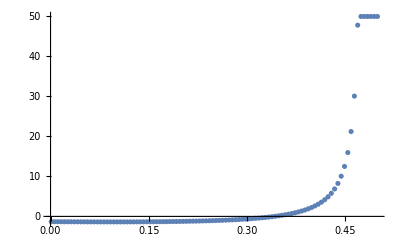

```mathematica
ListPlot[Table[{ymset[[i]],bphpexset[[i,1,1]]},{i,1,ncpt}],PlotRange->All]
```

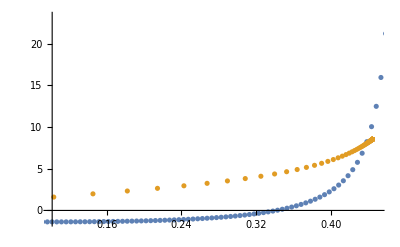

```mathematica
ListPlot[{Table[{ymset[[i]],bphpexset[[i,1,1]]},{i,1,ncpt}],Table[{compset[[i]],bphpinset[[i,1,1]]},{i,1,ncinpt}]},PlotRange->{{0.1,0.45},Automatic}]
```

```mathematica
(* interior *)
```

```mathematica
(* uniform star *)
```

```mathematica
et=1/3*1/Sqrt[1-2*comp];vf=(3*et*Sqrt[1-x^2]-1)/(2*(1-et*Sqrt[1-x^2]));xm=Sqrt[1-1/(9*et^2)];etscalareqin=Simplify[scalareq/.{w->3/2,v->vf,y->1/2 x^3}];
```

```mathematica
xmin=0.000001;xmax=0.99;
```

```mathematica
comp1=compset[[10000]];vfc=vf/.{x->0,comp->comp1};xm1=xm/.{comp->comp1};f21=-0.05;u21=5;etscalareqin1=etscalareqin/.{comp->comp1,f2->f21,u2->u21};solin=NDSolve[{etscalareqin1==0,bph[xmin]==1,bph'[xmin]==(8*f21*(1/2+vfc)+1/3*u21)*xmin},bph,{x,xmin,xmax}]
```

{{bph→                             -6
InterpolatingFunction[{{1. 10  , 0.99}}, <>]}}

```mathematica
bph'[x]/bph[x]/.solin[[1]]/.x->xm1
```

2.33841

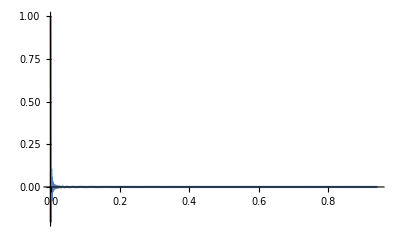

```mathematica
Plot[bph[x]/.solin[[1]],{x,xmin,xm1},PlotRange->All]
```

```mathematica
ncinpt=10000;ncinmin=0.001;ncinmax=N[4/9-0.000001];compset=Table[N[4/9-Exp[Log[4/9-ncinmin]+(Log[4/9-ncinmax]-Log[4/9-ncinmin])/(ncinpt-1)*(i-1)]],{i,1,ncinpt}];f2set={-0.1,-0.09,-0.08,-0.07,-0.06,-0.05,-0.04};u2set={0.1};bphpinset=Table[0,{i,1,ncinpt},{jr,1,Length[f2set]},{kr,1,Length[u2set]}];
```

```mathematica
AbsoluteTiming[Do[comp1=compset[[i]];vfc=vf/.{x->0,comp->comp1};xm1=xm/.{comp->comp1};f21=f2set[[jr]];u21=u2set[[1]];etscalareqin1=etscalareqin/.{comp->comp1,f2->f21,u2->u21};solin=NDSolve[{etscalareqin1==0,bph[xmin]==1,bph'[xmin]==(8*f21*(1/2+vfc)+1/3*u21)*xmin},bph,{x,xmin,xmax}];bphpinset[[i,jr,1]]=bph'[x]/bph[x]/.solin[[1]]/.x->xm1,{i,1,ncinpt},{jr,1,Length[f2set]}];]
```

$Aborted

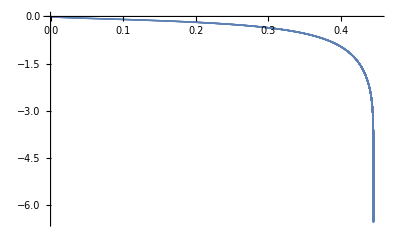

```mathematica
i1=1;i2=ncinpt;ListPlot[{Table[{compset[[i]],bphpinset[[i,1,1]]},{i,i1,i2}]},PlotRange->{{0,0.45},Automatic}]
```

```mathematica
Export["bphpint1_uni.dat",data]
```

```mathematica
bphpinset[[ncinpt,1,1]]
```

3.02408

```mathematica
ymset[[355]]
```

0.44479

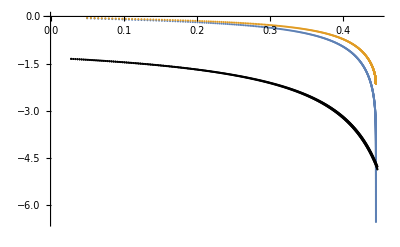

```mathematica
i1=10;i2=1000;i3=10;i4=360;ListPlot[{Table[{compset[[i]],bphpinset[[i,6,1]]},{i,i1,i2}],Table[{compset[[i]],bphpinset[[i,7,1]]},{i,i1,i2}],Table[{ymset[[i]],data[[i,6]]},{i,i3,i4}],Table[{ymset[[i]],data[[i,7]]},{i,i3,i4}]},PlotStyle->{ColorData[97,1],ColorData[97,2],Black,Black}]
```

```mathematica
data[[i4,5]]
```

-4.96078

```mathematica
data[[i4,4]]
```

-5.0473

```mathematica
data[[i4,3]]
```

-5.13296

```mathematica
data[[i4,2]]
```

-5.21778

```mathematica
data[[i4,1]]
```

-5.30179

```mathematica
(* plot using hpc data *)
```

```mathematica
ncpt=1000;ncinpt=10000;ymmin=0.001;ymmax=0.499;ncinmin=0.001;ncinmax=N[4/9-0.000001];ymset=Table[0.5-Exp[Log[0.5-ymmin]+(Log[0.5-ymmax]-Log[0.5-ymmin])/(ncpt-1)*(i-1)],{i,1,ncpt}];compset=Table[N[4/9-Exp[Log[4/9-ncinmin]+(Log[4/9-ncinmax]-Log[4/9-ncinmin])/(ncinpt-1)*(i-1)]],{i,1,ncinpt}];
```

```mathematica
datain1=Import["~/Yandex.Disk/Documents/research/kiaa/stgbns/data/linear/bphpintup1_uni.dat"];datain2=Import["~/Yandex.Disk/Documents/research/kiaa/stgbns/data/linear/bphpintup2_uni.dat"];datain3=Import["~/Yandex.Disk/Documents/research/kiaa/stgbns/data/linear/bphpintup3_uni.dat"];datain4=Import["~/Yandex.Disk/Documents/research/kiaa/stgbns/data/linear/bphpintup4_uni.dat"];datain5=Import["~/Yandex.Disk/Documents/research/kiaa/stgbns/data/linear/bphpintup5_uni.dat"];datain6=Import["~/Yandex.Disk/Documents/research/kiaa/stgbns/data/linear/bphpintup6_uni.dat"];datain7=Import["~/Yandex.Disk/Documents/research/kiaa/stgbns/data/linear/bphpintup7_uni.dat"];datain8=Import["~/Yandex.Disk/Documents/research/kiaa/stgbns/data/linear/bphpintup8_uni.dat"];datain9=Import["~/Yandex.Disk/Documents/research/kiaa/stgbns/data/linear/bphpintup9_uni.dat"];datain10=Import["~/Yandex.Disk/Documents/research/kiaa/stgbns/data/linear/bphpintup10_uni.dat"];
```

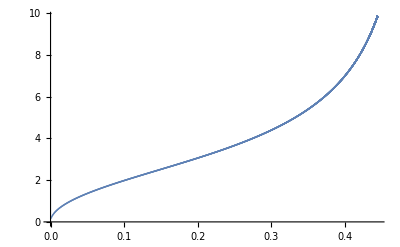

```mathematica
i1=1;i2=ncinpt;ListPlot[{Table[{compset[[i]],datain4[[i,5]]},{i,i1,i2}]},PlotRange->All]
```

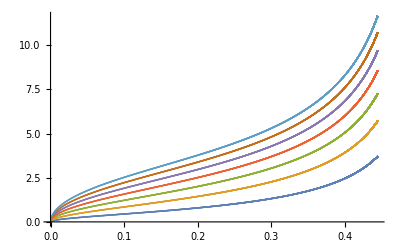

```mathematica
i1=1;i2=ncinpt;ListPlot[{Table[{compset[[i]],datain1[[i,1]]},{i,i1,i2}],Table[{compset[[i]],datain1[[i,2]]},{i,i1,i2}],Table[{compset[[i]],datain1[[i,3]]},{i,i1,i2}],Table[{compset[[i]],datain1[[i,4]]},{i,i1,i2}],Table[{compset[[i]],datain1[[i,5]]},{i,i1,i2}],Table[{compset[[i]],datain1[[i,6]]},{i,i1,i2}],Table[{compset[[i]],datain1[[i,7]]},{i,i1,i2}]},PlotRange->All]
```

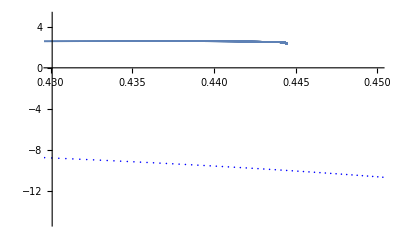

```mathematica
i1=1;i2=ncinpt;i3=1;i4=ncpt;jr1=6;ListPlot[{Table[{compset[[i]],datain7[[i,jr1]]},{i,i1,i2}],Table[{ymset[[i]],data7[[i,jr1]]},{i,i3,i4}]},PlotStyle->{{ColorData[97,1]},Blue},PlotRange->{{0.43,0.45},{-15,5}}]
```

```mathematica
data1=Import["~/Yandex.Disk/Documents/research/kiaa/stgbns/data/linear/bphpextup1.dat"];data2=Import["~/Yandex.Disk/Documents/research/kiaa/stgbns/data/linear/bphpextup2.dat"];data3=Import["~/Yandex.Disk/Documents/research/kiaa/stgbns/data/linear/bphpextup3.dat"];data4=Import["~/Yandex.Disk/Documents/research/kiaa/stgbns/data/linear/bphpextup4.dat"];data5=Import["~/Yandex.Disk/Documents/research/kiaa/stgbns/data/linear/bphpextup5.dat"];data6=Import["~/Yandex.Disk/Documents/research/kiaa/stgbns/data/linear/bphpextup6.dat"];data7=Import["~/Yandex.Disk/Documents/research/kiaa/stgbns/data/linear/bphpextup7.dat"];data8=Import["~/Yandex.Disk/Documents/research/kiaa/stgbns/data/linear/bphpextup8.dat"];data9=Import["~/Yandex.Disk/Documents/research/kiaa/stgbns/data/linear/bphpextup9.dat"];data10=Import["~/Yandex.Disk/Documents/research/kiaa/stgbns/data/linear/bphpextup10.dat"];
```

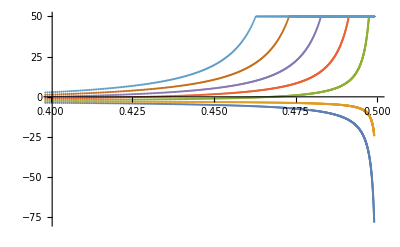

```mathematica
i1=1;i2=ncpt;ListPlot[{Table[{ymset[[i]],data5[[i,1]]},{i,i1,i2}],Table[{ymset[[i]],data5[[i,2]]},{i,i1,i2}],Table[{ymset[[i]],data5[[i,3]]},{i,i1,i2}],Table[{ymset[[i]],data5[[i,4]]},{i,i1,i2}],Table[{ymset[[i]],data5[[i,5]]},{i,i1,i2}],Table[{ymset[[i]],data5[[i,6]]},{i,i1,i2}],Table[{ymset[[i]],data5[[i,7]]},{i,i1,i2}]},PlotRange->{{0.4,0.5},All}]
```

```mathematica
data[[i2,7]]
```

-103.206

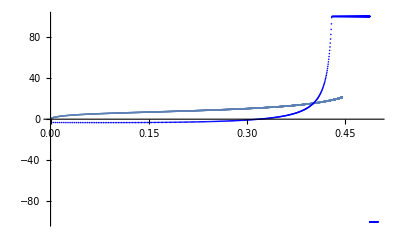

```mathematica
i1=1;i2=ncinpt;i3=1;i4=ncpt;jr1=4;ListPlot[{Table[{compset[[i]],datain7[[i,jr1]]},{i,i1,i2}],Table[{ymset[[i]],data7[[i,jr1]]},{i,i3,i4}]},PlotStyle->{{ColorData[97,1]},Blue},PlotRange->All]
```

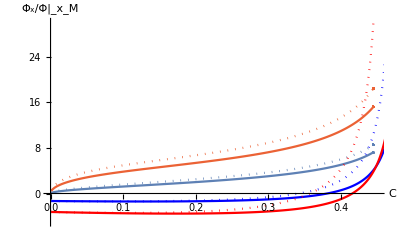

```mathematica
i1=1;i2=ncinpt;i3=1;i4=ncpt;ListPlot[{Table[{compset[[i]],datain1[[i,4]]},{i,i1,i2}],Table[{compset[[i]],datain1[[i,3]]},{i,i1,i2}],Table[{compset[[i]],datain7[[i,3]]},{i,i1,i2}],Table[{compset[[i]],datain7[[i,2]]},{i,i1,i2}],Table[{ymset[[i]],data1[[i,4]]},{i,i3,i4}],Table[{ymset[[i]],data1[[i,3]]},{i,i3,i4}],Table[{ymset[[i]],data7[[i,3]]},{i,i3,i4}],Table[{ymset[[i]],data7[[i,2]]},{i,i3,i4}]},PlotStyle->{{Dotted,ColorData[97,1]},{ColorData[97,1]},{Dotted,ColorData[97,4]},{ColorData[97,4]},{Dotted,Blue},Blue,{Dotted,Red},Red},PlotRange->{{0,0.45},{-5,30}},Joined->True,AxesLabel->{"C","Φ_x/Φ|_x_M"}]
```

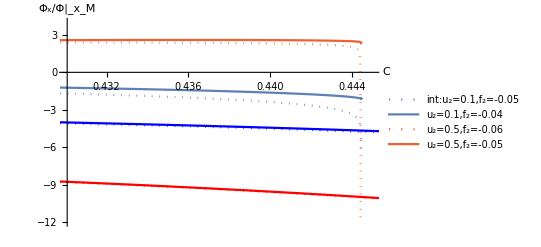

```mathematica
ListPlot[{Table[{compset[[i]],datain1[[i,6]]},{i,1000,10000}],Table[{compset[[i]],datain1[[i,7]]},{i,1000,10000}],Table[{compset[[i]],datain7[[i,5]]},{i,1000,7460}],Table[{compset[[i]],datain7[[i,6]]},{i,1000,10000}],Table[{ymset[[i]],data1[[i,6]]},{i,100,360}],Table[{ymset[[i]],data1[[i,7]]},{i,100,360}],Table[{ymset[[i]],data7[[i,5]]},{i,100,360}],Table[{ymset[[i]],data7[[i,6]]},{i,100,360}]},PlotStyle->{{Dotted,ColorData[97,1]},{ColorData[97,1]},{Dotted,ColorData[97,4]},{ColorData[97,4]},{Dotted,Blue},Blue,{Dotted,Red},Red},Joined->True,AxesLabel->{"C","Φ_x/Φ|_x_M"},PlotLegends->{"int:u_2=0.1,f_2=-0.05","u_2=0.1,f_2=-0.04","u_2=0.5,f_2=-0.06","u_2=0.5,f_2=-0.05"},PlotRange->{{0.43,0.445},{-12,4}}]
```